## Exercícios Lista 3

5.1 Make a list of the first 10 squares, in reverse order.

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

5.2 Find the total of the first 10 squares.

```mathematica
Total[Range[10]^2]
```

385

5.3 Make a plot of the first 10 squares, starting at 1.

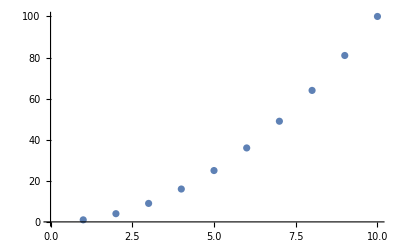

```mathematica
ListPlot[Range[10]^2]
```

5.4 Use Sort, Join and Range to create {1, 1, 2, 2, 3, 3, 4, 4}.

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

5.5 Use Range and + to make a list of numbers from 10 to 20, inclusive.

```mathematica
Range[11]+9
```

{10,11,12,13,14,15,16,17,18,19,20}

5.6 Make a combined list of the first 5 squares and cubes (numbers raised to the power 3), sorted into order

```mathematica
Sort[Join[Range[5]^2,Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

5.7 Find the number of digits in 2^128.

```mathematica
Length[IntegerDigits[2^128]]
```

39

5.8 Find the first digit of 2^32.

```mathematica
First[IntegerDigits[2^32]]
```

4

5.9 Find the first 10 digits in 2^100.

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

5.10 Find the largest digit that appears in 2^20.

```mathematica
Max[IntegerDigits[2^20]]
```

8

5.11 Find how many zeros appear in the digits of 2^1000.

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

5.12 Use Part, Sort and IntegerDigits to find the second-smallest digit in 2^20.

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

5.13 Make a line plot of the sequence of digits that appear in 2^128.

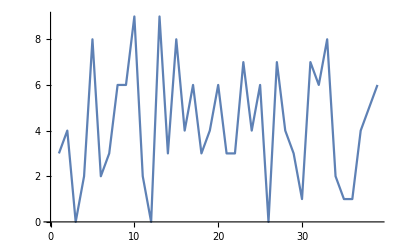

```mathematica
ListPlot[IntegerDigits[2^128],Joined->True]
```

5.14 Use Take and Drop to get the sequence 11 through 20 from Range[100].

```mathematica
Take[Drop[Range[100],10],10]
```

{11,12,13,14,15,16,17,18,19,20}

6.1 Make a list in which the number 1000 is repeated 5 times.

```mathematica
Table[1000,{5}]
```

{1000,1000,1000,1000,1000}

6.2 Make a table of the values of n^3 for n from 10 to 20.

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

6.3 Make a number line plot of the first 20 squares.

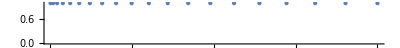

```mathematica
NumberLinePlot[Range[20]^2]
```

6.4 Make a list of the even numbers (2, 4, 6, ...) up to 20.

```mathematica
Range[2,20,2]
```

{2,4,6,8,10,12,14,16,18,20}

6.5 Use Table to get the same result as Range[10].

```mathematica
Table[n,{n,10}]
```

{1,2,3,4,5,6,7,8,9,10}

6.6 Make a bar chart of the first 10 squares.

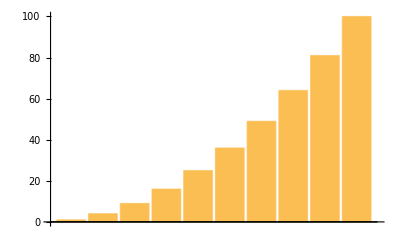

```mathematica
BarChart[Range[10]^2]
```

6.7 Make a table of lists of digits for the first 10 squares.

```mathematica
Table[IntegerDigits[n^2],{n,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

6.8 Make a list line plot of the length of the sequence of digits for each of the first 100 squares.

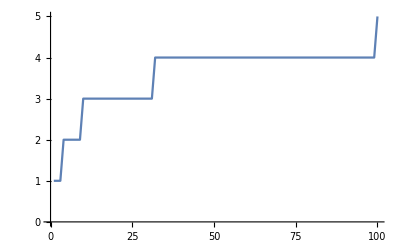

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,100}]]
```

6.9 Make a table of the first digit of the first 20 squares.

```mathematica
Table[First[IntegerDigits[n^2]],{n,20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

6.10 Make a list line plot of the first digits of the first 100 squares.

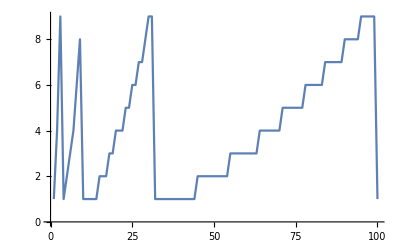

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,100}]]
```